# Vpliv pandemije COVID-19 na trg kriptovalut

## Kratek uvod

V tem projektu bom  poskušal ugotoviti, ali  lahko najdem kakšne informacije, ki bi nakazovale na morebiten vpliv pandemije Covid-19 na trg kriptovalut.
Enostavno povedano bi lahko rekli, da so kriptovalute virtualni denar, ki uporablja kriptografijo za varne transakcije in nadzor. Kar ločuje kriptovalute od navadnega
denarja je njihova decentralizirana narava - delujejo na tehnologiji imenovani blockchain, kar pomeni, da se transakcije in lastništvo kriptovalut beležijo in preverjajo s pomočjo 
omrežja računalnikov, namesto neke centralne “oblasti” kot je pri bankah. Prva in najbolj znana kriptovaluta je Bitcoin, ki se je prvič pojavila leta 2009, kot avtor pa je anonimna oseba
Satoshi Nakamoto.
Spodaj primera podatkov o bitcoinu in dve dejanski denarnici.

```mathematica
BlockchainData[BlockchainBase->"Bitcoin"]//Dataset
```

```mathematica
BlockchainAddressData["34xp4vRoCGJym3xR7yCVPFHoCNxv4Twseo",BlockchainBase->"Bitcoin"]//Dataset
```

```mathematica
0x00000000219ab540356cBB839Cbe05303d7705Fa
```

```mathematica
BlockchainAddressData["0x00000000219ab540356cBB839Cbe05303d7705Fa",BlockchainBase->"Ethereum"]//Dataset
```

## Pridobivanje in predstavitev podatkov

pridobivanje podatkov s strani yahoo finance in wolfram Financial data.

```mathematica
AbsoluteTiming[lsData=Import["https://finance.yahoo.com/cryptocurrencies","Data"];];
pos=First@Position[lsData,{"Symbol","Name","Price (Intraday)","Change","% Change",___}];
imenaStolpcev=lsData[[Sequence@@pos]];
Length[imenaStolpcev];
podatki=lsData[[Sequence@@Append[Most[pos],2]]];
Dimensions[podatki];
podatki=Dataset[podatki][All,AssociationThread[imenaStolpcev[[1;;-3]],#]&]
```

```mathematica
AbsoluteTiming[ccNow=Round@AbsoluteTime[Date[]]-AbsoluteTime[{1970,1,1,0,0,0}];
aCryptoCurrenciesDataRaw=Association@Map[#->ResourceFunction["ImportCSVToDataset"]["https://query1.finance.yahoo.com/v7/finance/download/"<>#<>"?period1=1410825600&period2="<>ToString[ccNow]<>"&interval=1d&events=history&includeAdjustedClose=true"]&,Normal[dsCryptoCurrencies[All,"Symbol"]]];]
Dimensions/@aCryptoCurrenciesDataRaw;
AbsoluteTiming[aCryptoCurrenciesData=Association@KeyValueMap[Function[{k,v},k->v[All,Join[<|"Symbol"->k,"DateObject"->DateObject[#Date]|>,#]&]],aCryptoCurrenciesDataRaw];];
ResourceFunction["RecordsSummary"][Join@@Values[aCryptoCurrenciesData],"MaxTallies"->30]
```

{3.95756,Null}

{1 Symbol
BTC-USD | 3272
LTC-USD | 3272
ADA-USD | 2123
BCH-USD | 2123
BNB-USD | 2123
DOGE-USD | 2123
ETH-USD | 2123
LINK-USD | 2123
TRX-USD | 2123
USDT-USD | 2123
XLM-USD | 2123
XRP-USD | 2123
USDC-USD | 1790
WBTC-USD | 1676
MATIC-USD | 1588
LEO-USD | 1565
DAI-USD | 1380
SOL-USD | 1240
AVAX-USD | 1146
SHIB-USD | 1127
DOT-USD | 1108
STETH-USD | 983
TON11419-USD | 736
WTRX-USD | 546
WKAVA-USD | 156,2 DateObject
Min | Wed 17 Sep 2014 00:00:00GMT+2
1st Qu | Tue 13 Aug 2019 00:00:00GMT+2
Mean | Tue 24 Nov 2020 17:54:30GMT+2
Median | Mon 8 Mar 2021 00:00:00GMT+2
3rd Qu | Sun 19 Jun 2022 00:00:00GMT+2
Max | Fri 1 Sep 2023 00:00:00GMT+2,3 Date
2023-03-30 | 25
2023-03-31 | 25
2023-04-01 | 25
2023-04-02 | 25
2023-04-03 | 25
2023-04-04 | 25
2023-04-05 | 25
2023-04-06 | 25
2023-04-07 | 25
2023-04-08 | 25
2023-04-09 | 25
2023-04-10 | 25
2023-04-11 | 25
2023-04-12 | 25
2023-04-13 | 25
2023-04-14 | 25
2023-04-15 | 25
2023-04-16 | 25
2023-04-17 | 25
2023-04-18 | 25
2023-04-19 | 25
2023-04-20 | 25
2023-04-21 | 25
2023-04-22 | 25
2023-04-23 | 25
2023-04-24 | 25
2023-04-25 | 25
2023-04-26 | 25
2023-04-27 | 25
(Other) | 42090,4 Open
0. | 259
8.×10^-6 | 133
9.×10^-6 | 96
0.000011 | 96
0.000012 | 86
0.00001 | 70
null | 69
7.×10^-6 | 63
0.000013 | 38
6.×10^-6 | 23
0.000024 | 17
0.000022 | 16
0.000026 | 15
0.000025 | 14
0.000023 | 13
0.000027 | 13
0.000031 | 13
0.000021 | 12
0.000028 | 12
2.×10^-6 | 11
0.99996 | 10
1.00008 | 10
1.0001 | 10
1.×10^-6 | 9
0.000034 | 9
1.00004 | 9
1.00006 | 9
0.000014 | 8
0.000029 | 8
(Other) | 41664,5 High
0. | 258
8.×10^-6 | 127
9.×10^-6 | 104
0.000011 | 97
0.000012 | 85
null | 69
0.00001 | 63
7.×10^-6 | 52
0.000013 | 50
1.0002 | 50
0.000025 | 23
0.000014 | 17
0.000022 | 17
2.×10^-6 | 13
1.0002 | 13
1.002 | 13
0.000023 | 12
0.000028 | 12
0.000029 | 12
0.000027 | 11
0.000032 | 11
6.×10^-6 | 10
0.000024 | 10
0.000026 | 10
1.002 | 9
0.000031 | 8
0.00003 | 7
0.000034 | 7
0.000035 | 7
(Other) | 41638,6 Low
0. | 259
8.×10^-6 | 134
0.000011 | 92
0.00001 | 89
7.×10^-6 | 85
9.×10^-6 | 77
0.000012 | 77
null | 69
0.9998 | 48
6.×10^-6 | 33
0.000013 | 24
0.000024 | 18
0.999801 | 18
0.000022 | 16
0.000023 | 16
0.000026 | 15
1.×10^-6 | 14
0.000025 | 13
0.000028 | 13
0.00002 | 12
0.000021 | 12
0.000033 | 10
0.000014 | 9
0.000027 | 9
2.×10^-6 | 7
0.000029 | 7
0.000034 | 7
0.99994 | 7
0.000015 | 6
(Other) | 41619,7 Close
0. | 258
8.×10^-6 | 133
9.×10^-6 | 95
0.000011 | 95
0.000012 | 86
0.00001 | 71
null | 69
7.×10^-6 | 65
0.000013 | 38
6.×10^-6 | 23
0.000024 | 17
0.000022 | 16
0.000026 | 15
0.000025 | 14
0.000031 | 14
0.000023 | 13
0.000027 | 13
0.000021 | 12
0.000028 | 12
2.×10^-6 | 11
1.×10^-6 | 9
0.000034 | 9
0.999962 | 9
1.00001 | 9
1.00005 | 9
1.00009 | 9
1.00009 | 9
0.000014 | 8
0.000029 | 8
(Other) | 41666,8 Adj Close
0. | 258
8.×10^-6 | 133
9.×10^-6 | 95
0.000011 | 95
0.000012 | 86
0.00001 | 71
null | 69
7.×10^-6 | 65
0.000013 | 38
6.×10^-6 | 23
0.000024 | 17
0.000022 | 16
0.000026 | 15
0.000025 | 14
0.000031 | 14
0.000023 | 13
0.000027 | 13
0.000021 | 12
0.000028 | 12
2.×10^-6 | 11
1.×10^-6 | 9
0.000034 | 9
0.999962 | 9
1.00001 | 9
1.00005 | 9
1.00009 | 9
1.00009 | 9
0.000014 | 8
0.000029 | 8
(Other) | 41666,9 Volume
0 | 123
null | 69
9 | 4
13 | 3
36 | 3
5446317941 | 3
2 | 2
6 | 2
8 | 2
10 | 2
45 | 2
109 | 2
158 | 2
172 | 2
304 | 2
426 | 2
429 | 2
599 | 2
763 | 2
1881 | 2
7745 | 2
784796 | 2
1211900 | 2
2783960 | 2
7602413 | 2
12387900 | 2
14529600 | 2
15499400 | 2
26124800 | 2
(Other) | 42564}

### Grafična predstavitev podatkov

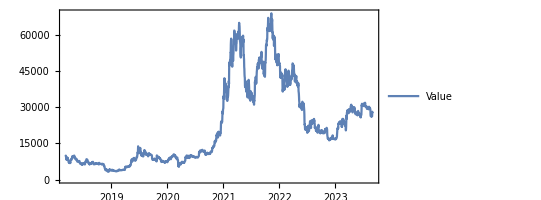
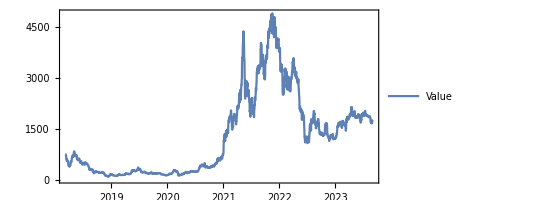
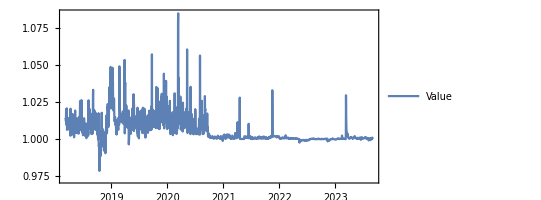
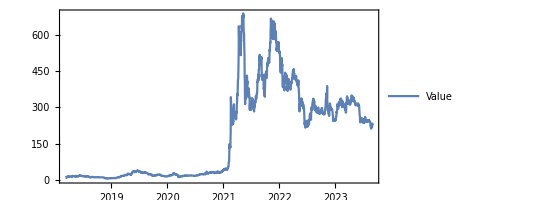
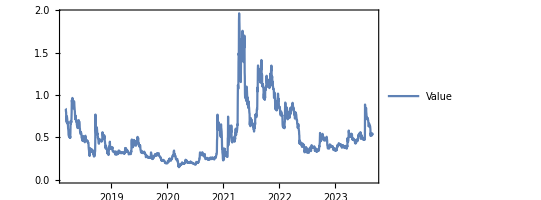
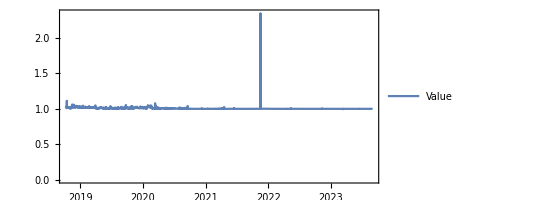
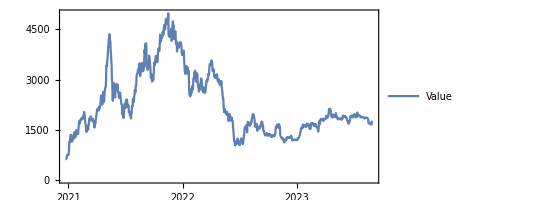
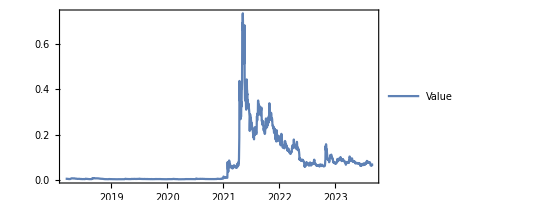
<|BTC-USD→-Graphics-,ETH-USD→-Graphics-,USDT-USD→-Graphics-,BNB-USD→-Graphics-,XRP-USD→-Graphics-,USDC-USD→-Graphics-,STETH-USD→-Graphics-,DOGE-USD→-Graphics-,ADA-USD→-Graphics-,SOL-USD→-Graphics-,WTRX-USD→-Graphics-,WKAVA-USD→-Graphics-,TRX-USD→-Graphics-,TON11419-USD→-Graphics-,DOT-USD→-Graphics-,DAI-USD→-Graphics-,MATIC-USD→-Graphics-,LTC-USD→-Graphics-,SHIB-USD→-Graphics-,WBTC-USD→-Graphics-,BCH-USD→-Graphics-,AVAX-USD→-Graphics-,LEO-USD→-Graphics-,XLM-USD→-Graphics-,LINK-USD→-Graphics-|>

```mathematica
nDays=2000;
Map[Block[{dsTemp=#[Select[AbsoluteTime[#DateObject]>AbsoluteTime[DatePlus[Now,-Quantity[nDays,"Days"]]]&]]},DateListPlot[{Normal[dsTemp[All,{"DateObject","High"}][Values]]},PlotLegends->{"Value"},AspectRatio->1/2,PlotRange->All]]&,aCryptoCurrenciesData]
```

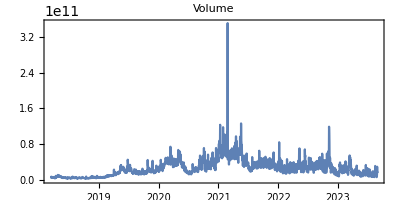
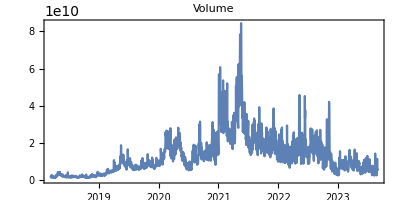
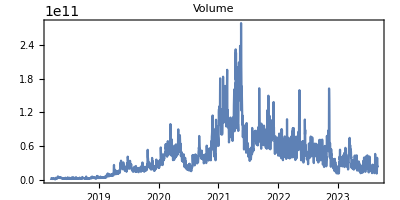
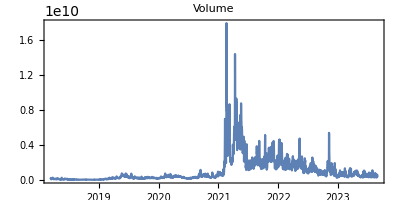
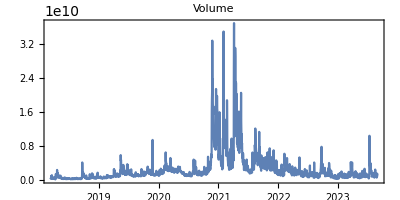
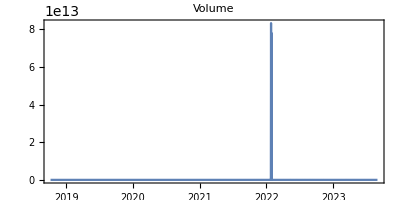
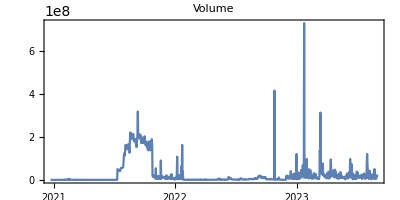
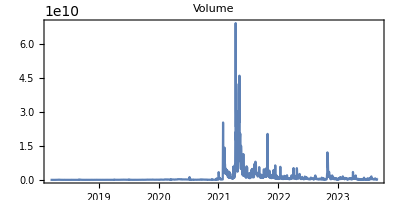
<|BTC-USD→-Graphics-,ETH-USD→-Graphics-,USDT-USD→-Graphics-,BNB-USD→-Graphics-,XRP-USD→-Graphics-,USDC-USD→-Graphics-,STETH-USD→-Graphics-,DOGE-USD→-Graphics-,ADA-USD→-Graphics-,SOL-USD→-Graphics-,WTRX-USD→-Graphics-,WKAVA-USD→-Graphics-,TRX-USD→-Graphics-,TON11419-USD→-Graphics-,DOT-USD→-Graphics-,DAI-USD→-Graphics-,MATIC-USD→-Graphics-,LTC-USD→-Graphics-,SHIB-USD→-Graphics-,WBTC-USD→-Graphics-,BCH-USD→-Graphics-,AVAX-USD→-Graphics-,LEO-USD→-Graphics-,XLM-USD→-Graphics-,LINK-USD→-Graphics-|>

```mathematica
nDays=2000;
Map[Block[{dsTemp=#[Select[AbsoluteTime[#DateObject]>AbsoluteTime[DatePlus[Now,-Quantity[nDays,"Days"]]]&]]},DateListPlot[{Normal[dsTemp[All,{"DateObject","Volume"}][Values]]},PlotLabel->"Volume",AspectRatio->1/2,PlotRange->All]]&,aCryptoCurrenciesData]
```

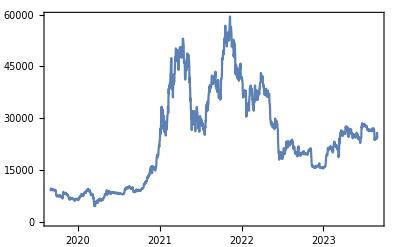

```mathematica
DateListPlot@FinancialData["BTC/EUR",{Now-Quantity[48,"Months"],Now}]
```

```mathematica
DateListPlot@FinancialData["ETH/EUR",{Now-Quantity[48,"Months"],Now}]
```

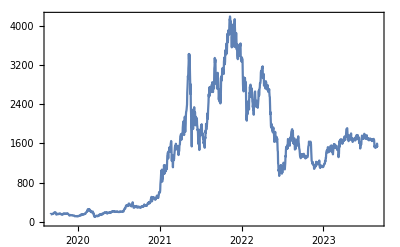

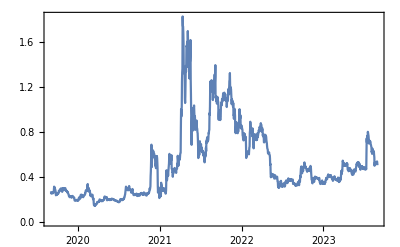

```mathematica
DateListPlot@FinancialData["XRP/USD",{Now-Quantity[48,"Months"],Now}]
```

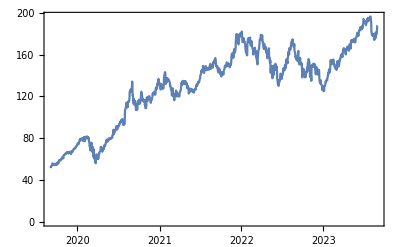

```mathematica
DateListPlot@FinancialData["AAPL",{Now-Quantity[48,"Months"],Now}]
```

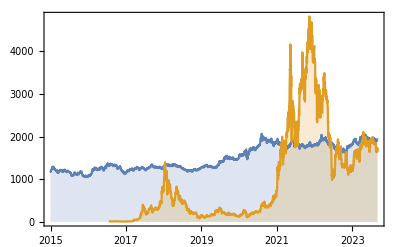

```mathematica
DateListPlot[{FinancialData["XAU/USD",{2015}],FinancialData["ETH/USD",{2015}]},Joined->True,Filling->Bottom]
```

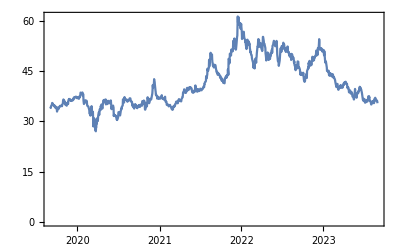

```mathematica
DateListPlot@FinancialData["Pfizer",{Now-Quantity[48,"Months"],Now}]
```

## Aplikacija v oblaku

```mathematica
Pretvornik=CurrencyConvert[Interpreter["CurrencyAmount"][#amount],Interpreter["CurrencyName"][#currency]]&;
```

```mathematica
form=FormPage[{"amount"-><|"Label"->"Stevilo in 1. valuta","Help"->"Primer: 10 bitcoins"|>,"currency"-><|"Label"->"Ime valute v katero zelite pretvoriti","Help"->"Primer: Us dollar"|>},converter,PageTheme->"Black",AppearanceRules-><|"Title"->"Pretvornik kriptovalut","Description"->"Vnesite stevilo in valuto iz katere zelite pretvarjati, ter v katero valuto","SubmitLabel"->"Convert!"|>];
CloudDeploy[form,"Pretvornik",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/vidko021/Pretvornik]